```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Problem 1*)
testList = Range/@Range[25];
triangular[n_/;((Dimensions[n][[1]]-Length[n]===0)||(Dimensions[n][[1]]-Length[n]===1))]:=Module[{num,list},list=Cases[n,k_/;OddQ[Count[k,_?OddQ]]];num=Table[Count[list[[x]],_?EvenQ],{x,Length[list]}];{num,list}//Transpose//MatrixForm]
triangular[testList]
```

(0 | {1}
1 | {1,2}
2 | {1,2,3,4,5}
3 | {1,2,3,4,5,6}
4 | {1,2,3,4,5,6,7,8,9}
5 | {1,2,3,4,5,6,7,8,9,10}
6 | {1,2,3,4,5,6,7,8,9,10,11,12,13}
7 | {1,2,3,4,5,6,7,8,9,10,11,12,13,14}
8 | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}
9 | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}
10 | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}
11 | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}
12 | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25})

```mathematica
(*Problem 2*)
Clear[piDig,subseq]
piDig=FromDigits[First[RealDigits[π,10,10^7,-1]]];
subseq=FromDigits[{3,1,4,1,5,9}];
findSubseq[longInteger_?IntegerQ,subseq_?IntegerQ]:=Module[{positions},positions=Position[Partition[IntegerDigits[longInteger],Length[IntegerDigits[subseq]],1],IntegerDigits[subseq]]/.{num_?IntegerQ}:>{num,num+Length[subseq//IntegerDigits]-1};Print[TableForm[{{positions[[All,1]]//Column,positions[[All,2]]//Column}},TableHeadings->{None,{"starting position", "ending position"}}],"\nthe number of occurences of the given subsequence 314159 inside the source integer is ",Length[positions]]]
findSubseq[piDig,subseq]
```

starting position | ending position
176451
1259351
1761051
6467324
6518294
9753731
9973760 | 176456
1259356
1761056
6467329
6518299
9753736
9973765
the number of occurences of the given subsequence 314159 inside the source integer is 7

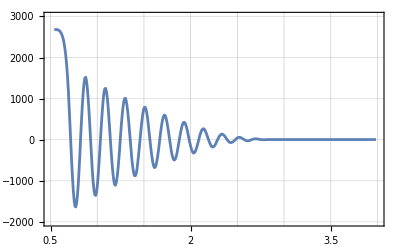

```mathematica
(*Problem 3*)
(*Prep Work*)
file=Import["C:\\Users\\natha\\OneDrive\\Desktop\\AME405\\HW\\Free_M474&509.csv"];
data=Drop[file[[All,{2,4}]],1];
Diff=Differences[data[[All,2]][[Range[70]]]];
positions = Position[Abs[Diff],n_/;(n<3)];
trimmedData=Drop[data,Length[Flatten[positions]]];
ListLinePlot[trimmedData,GridLines->{{0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5},Automatic},FrameTicks->{{0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7},Automatic},PlotRange->{{.5,4},{-2000,3000}},Frame->True]
```

Solving Problem 3
After offset removal the following response is plotted:

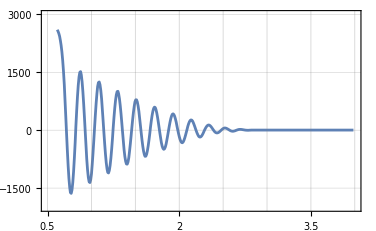

```mathematica
removeOffset[data_?StringQ]:=Module[{file,dataset,diffs,pos,trimmed},file=Import[data];dataset=Drop[file,1];diffs=Differences[dataset[[All,2]][[Range[70]]]];pos=Position[Abs[diffs],n_/;(n<3)];trimmed=Drop[dataset,Length[Flatten[pos]]];trimmed[[All,{2,4}]]]
dataOffsetRemoved=removeOffset["C:\\Users\\natha\\OneDrive\\Desktop\\AME405\\HW\\Free_M474&509.csv"];
plot = ListLinePlot[dataOffsetRemoved,GridLines->{{0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5},Automatic},FrameTicks->{{0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7},Automatic},PlotRange->{{0.5,4},{-2000,3000}},Frame->True];
Print[Style["Solving Problem ",Italic,Purple,Bold,FontSize->16,FontFamily->"Times New Roman"],Style["3\n",Purple,Bold,FontSize->16],"After offset removal the following response is plotted:\n"]
Print[plot]
```

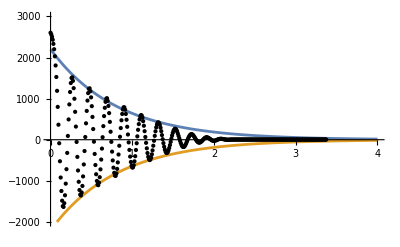

```mathematica
(*Extra Credit*)
(*Prep Work*)
Clear[shifted,peaks,coeffs,modelFit,a,b,t]
shifted=TimeSeriesShift[dataOffsetRemoved,-First[dataOffsetRemoved[[All,1]]]];
peaks=FindPeaks[shifted[[All,2]]];
peaks=peaks[[Range[2,9,1]]];
Table[peaks[[n,1]]=shifted[[peaks[[n,1]],1]],{n,Range[Length[peaks]]}];
coeffs=FindFit[peaks,a*ⅇ^(b*t),{a,b},t];
modelFit[t_]:=a*ⅇ^(b*t)/.coeffs;
Plot[{modelFit[t],-modelFit[t]},{t,0,4},Epilog->Map[Point,shifted],PlotRange->{-2000,3000}]
```

Amplitude of Response decays exponentially, with the rate
 ±2203.38 ⅇ^(-1.23479 t)

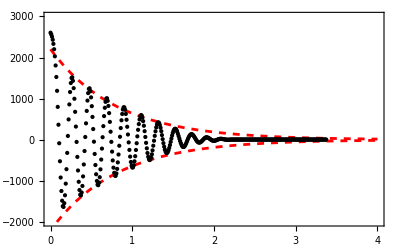

```mathematica
ClearAll[shifted, peaks]
fitExpCurve[n_?ListQ/;Head[n[[1]]]==List]:=Module[{shifted,allPeaks,peaks,coeffs,modelFit,coeffVals},shifted=TimeSeriesShift[n,-First[n[[All,1]]]];allPeaks=FindPeaks[shifted[[All,2]]];peaks=allPeaks[[Range[2,9,1]]];
Table[peaks[[x,1]]=shifted[[peaks[[x,1]],1]],{x,Range[Length[peaks]]}];
coeffs=FindFit[peaks,a*ⅇ^(b*t),{a,b},t];modelFit[t_]:=a*ⅇ^(b*t)/.coeffs;coeffVals=Values[coeffs];Print["Amplitude of Response decays exponentially, with the rate\n ±",coeffVals[[1]],Superscript[ⅇ,coeffVals[[2]]t]];Plot[{modelFit[t],-modelFit[t]},{t,0,4},Epilog->Map[Point,shifted],PlotRange->{-2000,3000},PlotStyle->{{Dashed,Red},{Dashed,Red}},Frame->True]]
fitExpCurve[dataOffsetRemoved]
```